#### 求出共振态贡献。

```mathematica
Clear[a, pts, plotsub, plotfull, f1, cont, contsubtract, s0]
Λ=0.1;s0=1.5; up=13;
M2min=0.4; M2max=1.6; dM2=0.05;

a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=3/2 M2(1+a[M2]/π+0.1 (0.6/M2)^2-0.14(0.6/M2)^3)
f2[M2_]:=(3 M2^2)/2(1+a[M2]/π-0.1(0.6/M2)^2+0.28(0.6/M2)^3)
cont1[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)ⅆs//N
cont2[M2_]:=∫_s0^up 3/2(1+a[s]/π)E^(-s/M2)sⅆs//N
m2[M2_]:=(f2[M2]-cont2[M2])/(f1[M2]-cont1[M2])
Timing[
pts = Table[m2[M2],{M2, M2min, M2max, dM2}] ;
]
data=Transpose[Join[{Range[M2min, M2max, dM2]}, {pts}]];
plot=ListLinePlot[data];
```

{84.194,Null}

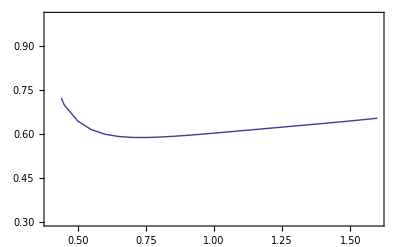

```mathematica
Show[plot,PlotRange->{{M2min,M2max},{0.3,1.0}},
AxesOrigin->{0.3,0.4}, Frame->True, Axes->False]
```